# Report Project 1

Course code: IX1500
Date: 2018-09-14

Maher Jabbar , Maherj@kth.se	
Simon Lagerqvist , simlag@kth.se

Task : (a)  Probability  using Census method

## Summery

### Task

Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck   of cards. The subset considered is cards valued 9,10,J,Q,K,A from the two decks, in total 48 cards.
Calculate the exact probability of the following hands using the  census method.
● one pair
● two pairs
● three of a kind
● four of a kind
● five of a kind
● full hand
● straight
● flush
● straight flush
● nothing
If a given hand contains different valued hands only one (the highest rank) is considered.
 Example :
 h={♣10,♡10,♢K,♢K,♠K}
 ⇒onepairQ(h)=false,twopairsQ(h)=false,threeofakindQ(h)=false,fullhandQ(h)=true
 Notice that the different sets of hands are supposed to be pairwise disjoint, e.g. {three of a kind}∩{full house}=∅. Check all different possibilities. This is an easy way of discover programming errors.
Compare and discuss the probabilities of the above variant poker game to the probabilities for a normal poker game with a standard 52 card deck.

### Result

Total of hands (2 decks/48 cards)  = 1712304 combinations of 5 cards
Total of hands (1 deck/52 cards) = Binomial[52, 5] = 2598960 combinations of 5 cards  

             Hand |         Probability
(2 decks/48 cards) |        Probability
(1 deck/52 cards)
One pair | 50.121% | 42.257%
Two pairs | 21.949% | 4.754%
Three of a kind | 12.558% | 2.113%
Four of a kind | 0.981% | 0.024%
Five of a kind | 0.019% | 0%
Full Hand | 2.747% | 0.144%
Straight | 3.812% | 0.392%
Flush | 0.170% | 0.196%
Straight Flush | 0.015% | 0.0015%
Nothing | 7.624% | 50.118%
Total | 99.998% | 99.999%

From the table, we can conclude some notes:
1. For 2 decks, the sets of equal cards become more common and more hands become possible (as in five of a kind).
2. The reason of zero probability in five of a kind hand (in normal poker game/ 52 card deck) because we have only 4 suits and its impossible to get 5 cards with the same rank (except of course the case that we have Joker card).
3. Due to extension each rank from 4 to 8, the combination of most of hands (except flush hand case) have increased.
4. The reason of low probability of flush hand in the 2 decks case is because we use only 6 cards out of 13 which decreases the chance of occurring hands of non-sequential ranks.

## Probability using census method

### The Model This section shows the definitions of each hand (5-card) that can be made from 2 decks poker game (24 cards for each deck) ● one pair In this hand, two cards are of the same rank (regardless of the suit type) while the other three cards all having different ranks from each other and from that of the pair. Example: {♣A, ♡A, ♢K, ♠9, ♡10} ● two pairs In this hand, two pairs of two cards are of the same rank (the ranks of each pair are different in rank, to avoid a four of a kind case). Example: {♢Q, ♡Q, ♣9, ♡K, ♡10} ● three of a kind In this hand, three cards are all of the same rank and other two are each of different ranks from the three cards and each other. Example: {♣J, ♡J, ♢J, ♠9, ♡10} ● four of a kind In this hand, four cards are all of the same rank while the fifth card has different rank from the four cards. Example: {♣A, ♡A, ♢A, ♠A, ♡10} ● five of a kind In this hand, five cards are all of the same rank . Example: {♣10, ♡10, ♢10, ♠10, ♡10} ● full hand This hand consists of one pair and a three of a kind of a different rank than the pair. Example: {♣A, ♡A, ♢K, ♠K, ♡K} ● straight In this hand, all five cards are sequential in rank but are not all of the same suit. Example: {♣9, ♡10, ♢J, ♠Q, ♡K} ● flush In this hand, all five cards are of the same suit but not all sequential in rank. Example: {♣A, ♣9, ♣K, ♣10, ♣10} ● straight flush In this hand, all five cards are of the same suit and are sequential in rank. Example: {♣9, ♣10, ♣J, ♣Q, ♣K} ● nothing In this hand, each card is of a different rank than any other card and not all five are of the same suit or sequential in rank (i.e none of the previous hands has occurred)

## Code

1. Two decks/48 cards code

```mathematica
ClearAll["`*"]
```

● Total hands in 2 decks (24 cards each)

```mathematica
(** 6 cards deck/total 24 cards **)
onedeck=Join[Table[spades[i],{i,9,14}],Table[clubs[i],{i,9,14}], Table[hearts[i],{i,9,14}],Table[diamonds[i],{i,9,14}]];  
twodecks = Join[onedeck, onedeck];  (** 2 decks/total 48 cards **)
rankQ[card1_, card2_]:= card1[[1]]<=card2[[1]];
rankSort[hand_] := Sort[hand, rankQ] 
hands = rankSort/@Subsets[twodecks, {5}]; 
totalhands=Length[hands]
```

1712304

● Straight flush

```mathematica
sameSuit[{_spades..}]:=True;
sameSuit[{_clubs..}]:=True;
sameSuit[{_hearts..}]:=True;
sameSuit[{_diamonds..}]:=True;
sameSuit[_]:=False;
straightflush[hand_]:=(sameSuit[hand])&&With[{values=First/@hand}, values-values[[1]]=={0,1,2,3,4}]
straightflushhands=Count[hands, _?(straightflush)] 
N[straightflushhands/totalhands] * 100
```

256

0.0149506

● Straight

```mathematica
straight[hand_]:=(!sameSuit[hand])&&With[{values=First/@hand}, values-values[[1]]=={0,1,2,3,4}]
straighthands=Count[hands, _?(straight)]
N[straighthands/totalhands] * 100
```

65280

3.81241

● Flush

```mathematica
flush[hand_]:=(sameSuit[hand])&&With[{values=First/@hand}, values-values[[1]]≠{0,1,2,3,4}]
flushhands=Count[hands, _?(flush)]
N[flushhands/totalhands] * 100
```

2912

0.170063

● Five of a kind

```mathematica
fiveQ[{_[x_]..}]:=True;
fiveQ[_]:=False
fivehands=Count[hands, _?(fiveQ)]
N[fivehands/totalhands] * 100
```

336

0.0196227

● Four of a kind

```mathematica
fourQ[{_[x_]..}]:=False;
fourQ[{___, _[x_], _[x_], _[x_], _[x_], ___}]:=True;
fourQ[_]=False;
fourhands=Count[hands, _?(fourQ)]
N[fourhands/totalhands] * 100
```

16800

0.981134

● Full hand

```mathematica
fullhand[{_[x_],_[x_],_[x_],_[y_],_[y_]}/;x≠y]:=True;
fullhand[{_[x_],_[x_],_[y_],_[y_],_[y_]}/;x≠y]:=True;
fullhand[_]=False;
fullhandhands=Count[hands, _?(fullhand)]
N[fullhandhands/totalhands] * 100
```

47040

2.74718

● Three of a kind

```mathematica
threeQ[{___, _[x_], _[x_], _[x_], ___}]:=True;
threeQ[_]:=False;
three2[hand_]:=(!fullhand[hand])&&(!fourQ[hand])&&(!fiveQ[hand])&&(threeQ[hand])
threehands=Count[hands, _?(three2)]
N[threehands/totalhands] * 100
```

215040

12.5585

● Two pairs

```mathematica
twopairs[{_[z_],_[x_], _[x_], _[y_], _[y_]}/;x≠y]:=True;
twopairs[{_[x_], _[x_], _[y_], _[y_],_[z_]}/;x≠y]:=True;
twopairs[{_[x_], _[x_],_[z_], _[y_], _[y_]}/;x≠y]:=True;
twopairs[_]:=False;
twopairs2[hand_]:=(!fullhand[hand])&&(!threeQ[hand])&&(!sameSuit[hand])&&(twopairs[hand])
twopairshands=Count[hands, _?(twopairs2)]
N[twopairshands/totalhands] * 100
```

375840

21.9494

● One pair

```mathematica
onepair[{___, _[x_], _[x_], ___}]:=True;
onepair[_]:=False;
onepair2[hand_]:=(!sameSuit[hand])&&(!threeQ[hand])&&(!twopairs[hand])&&(onepair[hand])
onepairhands=Count[hands, _?(onepair2)]
N[onepairhands/totalhands] * 100
```

858240

50.1219

● Nothing

```mathematica
nothing[hand_]:=(!onepair[hand])&&(!sameSuit[hand])&&With[{values=First/@hand}, values-values[[1]]≠{0,1,2,3,4}]
nothinghands=Count[hands, _?(nothing)]
N[nothinghands/totalhands] * 100
```

130560

7.62481

2. Ordinary  poker 52 cards code (for comparison purpose)

● Total hands

```mathematica
ClearAll["`*"]
hands=Binomial[52,5]
```

2598960

● One pair

```mathematica
Binomial[13,1]*Binomial[4,2]*Binomial[12,3]*(Binomial[4,1])^3
N[%/hands]*100
```

1098240

42.2569

● Two pairs

```mathematica
Binomial[13,2]*(Binomial[4,2])^2*Binomial[11,1]*Binomial[4,1]
N[%/hands]*100
```

123552

4.7539

● Three of a kind

```mathematica
Binomial[13,1]*Binomial[4,3]*Binomial[12,2]*(Binomial[4,1])^2
N[%/hands]*100
```

54912

2.11285

● Full hand

```mathematica
Binomial[13,1]*Binomial[4,3]*Binomial[12,1]*Binomial[4,2]
N[%/hands]*100
```

3744

0.144058

● Four of a kind

```mathematica
Binomial[13,1]*Binomial[4,4]*Binomial[12,1]*Binomial[4,1]
N[%/hands]*100
```

624

0.0240096

● Straight flush

```mathematica
10*Binomial[4,1]
N[%/hands]*100
```

40

0.00153908

● Straight

```mathematica
10*(Binomial[4,1])^5-40 (** excluding straight flushes **)
N[%/hands]*100
```

10200

0.392465

● Flush

```mathematica
Binomial[4,1]*Binomial[13,5]-40 (** excluding straight flushes **)
N[%/hands]*100
```

5108

0.19654

● Nothing

```mathematica
(Binomial[13,5]-10)*(4^5-4)
N[%/hands]*100
```

1302540

50.1177

Task : (b)  Probability  using combinatorial calculus

## Summery

### Task

Consider the following combinatorial calculus of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.
n_value=Binomial[6, 1],n_(4cards)=Binomial[8, 4], n_last=Binomial[40, 1]
n_4=n_value n_(4cards)n_last=Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
∴P_4=n_4/n_tot=(Binomial[6, 1] Binomial[8, 4]Binomial[40, 1])/Binomial[48, 5]=16800/1712304≈0.981134
Now, verify this probability by your census in part a).

Add combinatorial calculus for flush, straight, full house and 3 of a kind to your report. Also verify these calculations by your census. 
Sometimes it is a good idea to divide the sub problem in disjoint parts and add probabilities, e.g. pair of 1’s and pair of 2’s etc.

### Result

Total of hands (2 decks/48 cards) = Binomial[48, 5] = 1712304 combinations of 5 cards

    Hand |         Probability
 (2 decks/48 cards)
 (census method) |                       Probability 
                (2 deck/48 cards)
 (combinatorial calculus)
Four of a kind | 0.981% | 0.981%
Flush | 0.170% | 0.170%
Straight | 3.812% | 3.812%
Full Hand | 2.747% | 2.747%
Three of a kind | 12.558% | 12.558%

From above table, we can see that all probabilities are mached for both methods.

## Probability using combinatorial calculus

### The Model ● Total hands Possible 5 cards selection = (48 5) ● Four of a kind (6 1) different ranks (four of a kind) (8 4) combinations (four of a kind) (5 1) different ranks (fifth card) (8 1) different cards of rank (fifth card) Possible hands selection = (6 1) (8 4) (5 1) (8 1) ● Flush (4 1) different suits (12 5) combinations of five cards Possible hands selection = (4 1) (12 5) - (straight flush ways) ● Straight (2 1) different straight (9-K and 10-A) (8 1) ways of getting each card Possible hands selection = (2 1) [(8 1)]^5 - (straight flush ways) ● Full hand (6 1) different ranks (for 3 cards of same rank) (8 3) combinations (for 3 cards of same rank) (5 1) different ranks (for 2 cards of same rank) (8 2) combinations (for 2 cards of same rank) Possible hands selection = (6 1) (8 3) (5 1) (8 2) ● Three of a kind (6 1) different ranks (three of a kind) (8 3) combinations (three of a kind) (8 1) different cards (fourth card) (8 1) different cards (fifth card) (5 2) combinations for ranks (fourth and fifth cards) Possible hands selection = (6 1) (8 3) (8 1) (8 1) (5 2) ● Straight flush (it will be subtracted from straight and flush hands) (2 1) different straight (9-K and 10-A) (4 1) different suits (2 1) ways of getting each card Possible hands selection = (2 1) (4 1) [(2 1)]^5

## Code

```mathematica
ClearAll["`*"]
```

● Total hands

```mathematica
hands=Binomial[48,5]
```

1712304

● Four of a kind

```mathematica
Binomial[6,1]*Binomial[8,4]*Binomial[5,1]*Binomial[8,1]
N[%/hands]*100
```

16800

0.981134

● Flush

```mathematica
Binomial[4,1]*Binomial[12,5]- Binomial[2,1]*Binomial[4,1]*(Binomial[2,1])^5
N[%/hands]*100
```

2912

0.170063

● Straight

```mathematica
Binomial[2,1]*(Binomial[8,1])^5 - Binomial[2,1]*Binomial[4,1]*(Binomial[2,1])^5
N[%/hands]*100
```

65280

3.81241

● Full hand

```mathematica
Binomial[6,1]*Binomial[8,3]*Binomial[5,1]*Binomial[8,2]
N[%/hands]*100
```

47040

2.74718

● Three of a kind

```mathematica
Binomial[6,1]*Binomial[8,3]*(Binomial[8,1])^2*Binomial[5,2]
N[%/hands]*100
```

215040

12.5585

Task : (c)  Probability of one pair using Monte Carlo method

## Summery

### Task

Estimate the probability of one pair using the Monte Carlo method. Draw a diagram that shows how the probability estimate stabilises with increasing sample size.

### Result

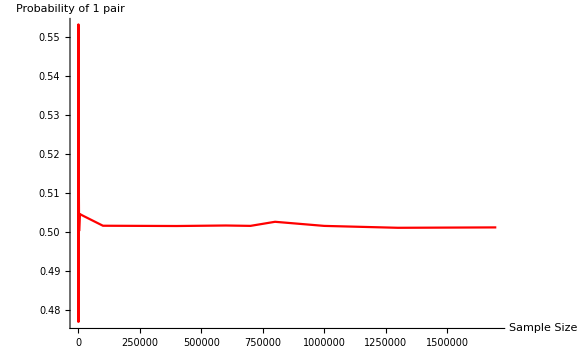

The above figure was taken from the output in the code section and we can see clearly the convergence of probability value when  sample size increases (i.e stabilises) and fixed at the value 0.501243 and this value is very closed to the value of one pair in Task (a).

                          Probability of One pair
     (2 decks/48 cards)
     (Census method) |   Probability  of One pair
         (2 deck/48 cards)
 (Monte Carlo method)
50.121% | 50.124%

## Monte Carlo method

### The Model

We will use the following steps to estimate the probability of one pair for different sample sizes using Monte Carlo method:
1. Creating a 2 decks (with 24 cards each) in the same way as in Task (a)
2. Creating a pair pattern with excluding the higher ranked combinations, then counting the possible one pair hands
3. Generate random samples from possible hands and Counting the number of one pairs in each sample
4. Selecting sample sizes where: 1 ≤  sample size  ≤ (48
5) 
5. Plotting the sample size vs probability of one pair counting.

## Code

● Creating a 2 decks with 24 cards each

```mathematica
ClearAll["`*"]
(** 6 cards deck/total 24 cards **)
onedeck=Join[Table[spades[i],{i,9,14}],Table[clubs[i],{i,9,14}], Table[hearts[i],{i,9,14}],Table[diamonds[i],{i,9,14}]];  
twodecks = Join[onedeck, onedeck];  (** 2 decks/total 48 cards **)
rankQ[card1_, card2_]:= card1[[1]]<=card2[[1]];
rankSort[hand_] := Sort[hand, rankQ] 
hands = rankSort/@Subsets[twodecks, {5}]; 
totalhands=Length[hands]
```

1712304

● Creating a pair pattern and counting the possible hands

```mathematica
onepair[{_spades..}]:=False; (** excluding flush **)
onepair[{_clubs..}]:=False;
onepair[{_hearts..}]:=False;
onepair[{_diamonds..}]:=False;
onepair[{___, _[x_], _[x_], _[x_], ___}]:=False; (** excluding 3 of a kind **)
onepair[{_[x_], _[x_],_[z_], _[y_], _[y_]}/;x≠y]:=False; (** excluding 2 pairs **)
onepair[{_[z_],_[x_], _[x_], _[y_], _[y_]}/;x≠y]:=False; 
onepair[{_[x_], _[x_], _[y_], _[y_],_[z_]}/;x≠y]:=False;
onepair[{___, _[x_], _[x_], ___}]:=True;  (** only 1 pair required **)
onepair[_]:=False;
NoOfPairs=Count[hands, _?(onepair)]
```

858240

●  Generate random samples and counting the number of one pairs

```mathematica
onepairSample[n_]:=RandomSample[hands, n]
onepairCount[n_]:=Count[onepairSample[n], _?(onepair)]
```

●  Selecting sample sizes

```mathematica
SampleSize = {100, 300, 700, 1000, 1500, 3000, 6000, 20000, 100000, 400000, 600000, 700000, 800000, 1000000, 1300000, 1700000}
Samples= {#, N[onepairCount[#]] / #}&/@SampleSize
```

{100,300,700,1000,1500,3000,6000,20000,100000,400000,600000,700000,800000,1000000,1300000,1700000}

{{100,0.44},{300,0.553333},{700,0.477143},{1000,0.522},{1500,0.516},{3000,0.500333},{6000,0.504667},{20000,0.5042},{100000,0.50167},{400000,0.5016},{600000,0.50173},{700000,0.501634},{800000,0.502683},{1000000,0.501628},{1300000,0.501142},{1700000,0.501243}}

●  Plotting the sample sizes

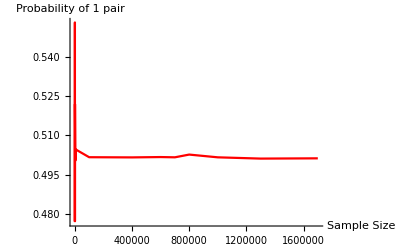

```mathematica
ListLinePlot[Samples, AxesLabel -> {"Sample Size","Probability of 1 pair"},PlotStyle->{Red}]
```